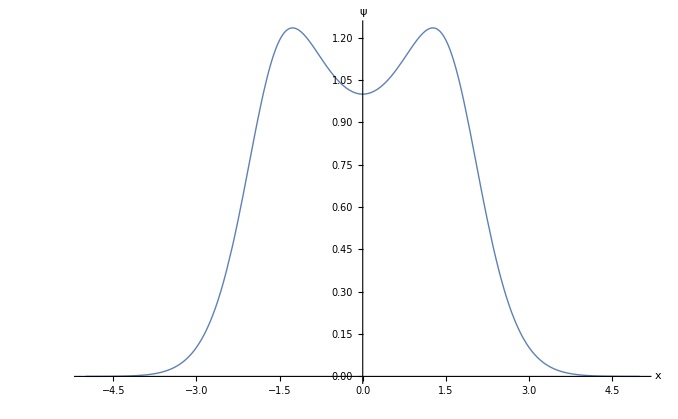

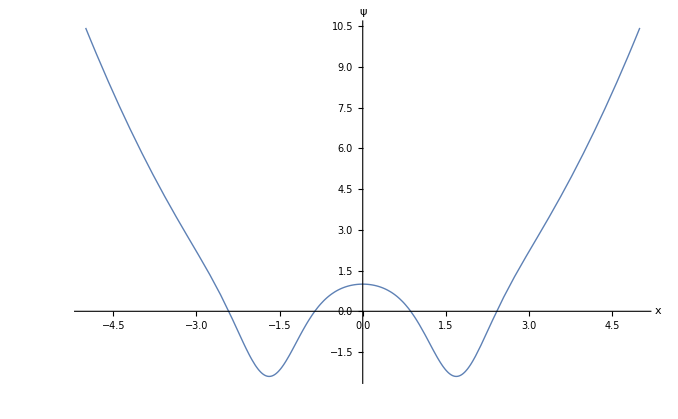

(√2 (Hypergeometric0F1[-1/4,x^4/16]^2-2 Hypergeometric0F1[-1/4,x^4/16] Hypergeometric0F1[3/4,x^4/16]+(1+x^2-x^4) Hypergeometric0F1[3/4,x^4/16]^2))/((x^2)^(5/4) BesselI[-1/4,x^2/2] Gamma[3/4])

```mathematica
(*Parametro a en funcion a El eigenvalor de la ecuación Hψ=En ψ*)
a[En_]:=-En/2 + 1/4;

(*Estados originales*)

(*Par*)
ψe[En_,x_] := Exp[-x^2/2] Hypergeometric1F1[a[En],1/2,x^2];

(*Impar*)
ψo[En_,x_] := x Exp[-x^2/2] Hypergeometric1F1[a[En]+1/2,3/2,x^2];
(*Potencial original*)
V0[x_]:=x^2/2;

(*funciones para calcular el nuevo potencial*)
σ[f_,x_] := D[f,x]/f;
dσ[f_,x_] := D[σ[f,x],x];
V1[f_,x_]:=V0[x] - 2 dσ[f,x];

(*Nuevos estados*)
ψ1[f_,g_,x_] := Wronskian[{f,g},x]/ f;





Plot[Evaluate[ψ1[ψe[1/4,x],ψo[1/4,x],x]],{x,-5,5},AxesLabel->{x,ψ},AxesStyle->Thick,PlotStyle->Thick, TicksStyle->Thick]
Plot[Evaluate[V1[ψe[1/4,x],x]],{x,-5,5},AxesLabel->{x,ψ}, AxesStyle->Thick,PlotStyle->Thick, TicksStyle->Thick]


(*Estado base dependiendo de las funcines semilla*)

ψ1[ψe[0,x],ψo[1,x],x]
```